# Wolfram/CodeEquivalenceUtilities

Utilities for testing code equivalence.

## Paclet

### Paclet Directory

NotebookDirectory[]

### Manifest

"DefinitionNotebook.nb"DefinitionNotebook.nb

"Documentation"

"English"

"Guides"

"CodeEquivalenceUtilities.nb"Documentation/English/Guides/CodeEquivalenceUtilities.nb

"ReferencePages"

"Symbols"

"CodeEquivalentQ.nb"Documentation/English/ReferencePages/Symbols/CodeEquivalentQ.nb

"EquivalenceTestData.nb"Documentation/English/ReferencePages/Symbols/EquivalenceTestData.nb

"FromCanonicalForm.nb"Documentation/English/ReferencePages/Symbols/FromCanonicalForm.nb

"MakeCanonicalForm.nb"Documentation/English/ReferencePages/Symbols/MakeCanonicalForm.nb

"ToCanonicalForm.nb"Documentation/English/ReferencePages/Symbols/ToCanonicalForm.nb

"Tutorials"

"AddingNewTransformationRules.nb"Documentation/English/Tutorials/AddingNewTransformationRules.nb

"Kernel"

"CachedValues.wl"Kernel/CachedValues.wl

"CanonicalForms"

"Attributes.wl"Kernel/CanonicalForms/Attributes.wl

"Common.wl"Kernel/CanonicalForms/Common.wl

"ExperimentalRules.wl"Kernel/CanonicalForms/ExperimentalRules.wl

"Graphics.wl"Kernel/CanonicalForms/Graphics.wl

"Rules.wl"Kernel/CanonicalForms/Rules.wl

"Scope.wl"Kernel/CanonicalForms/Scope.wl

"Structural.wl"Kernel/CanonicalForms/Structural.wl

"CodeEquivalenceUtilities.wl"Kernel/CodeEquivalenceUtilities.wl

"Debugging.wl"Kernel/Debugging.wl

"EvaluationControl.wl"Kernel/EvaluationControl.wl

"Formatting.wl"Kernel/Formatting.wl

"init.wl"Kernel/init.wl

"Types.wl"Kernel/Types.wl

"Utilities.wl"Kernel/Utilities.wl

"LICENSE"LICENSE

"PacletInfo.wl"PacletInfo.wl

"README.md"README.md

"Scripts"

"FormatNotebooks.wls"Scripts/FormatNotebooks.wls

"Tests"

"Attributes.wlt"Tests/Attributes.wlt

"Common.wlt"Tests/Common.wlt

"Data"

"EIWLData.wl"Tests/Data/EIWLData.wl

"EIWL.wlt"Tests/EIWL.wlt

"EvaluationControl.wlt"Tests/EvaluationControl.wlt

"Rules.wlt"Tests/Rules.wlt

## Web Content

### Headline Image

```mathematica
graph=Graph[{
a->x,
b->x,
a1->a,
a11->a1,
a12->a1,
a2->a,
a22->a2,
b1->b,
b2->b
},
EdgeStyle->Directive[Thickness[.03],GrayLevel[.85],Arrowheads[.15],Opacity[1]],
VertexSize->Medium,
VertexStyle->Directive[GrayLevel[.85],EdgeForm[None],Opacity[1]],
ImageSize->500,
AspectRatio->1
];
img=Show[HighlightGraph[graph,{Style[PathGraph[FindShortestPath[graph,b2,x],DirectedEdges->True],ColorData[97][1]],Style[PathGraph[FindShortestPath[graph,a22,x],DirectedEdges->True],ColorData[97][2]],
Style[x,ColorData[97][3]]},VertexLabels->{b2->Placed[Framed[Style[Defer@f[…],FontColor->ColorData[97][1],FontSize->36,FontWeight->Bold],Background->White,RoundingRadius->8,FrameMargins->8,FrameStyle->Directive[Thickness[5],ColorData[97][1]]],Center],a22->Placed[Framed[Style[Defer@g[…],FontColor->ColorData[97][2],FontSize->36,FontWeight->Bold],Background->White,RoundingRadius->8,FrameMargins->8,FrameStyle->Directive[Thickness[5],ColorData[97][2]]],Center],
x->Placed[Style["✓",FontWeight->Bold,FontSize->150,FontColor->ColorData[97][3]],{3.5,1.5}]
}],ImageSize->450,AspectRatio->1]/.{HoldPattern[f]->RawBoxes["f"],HoldPattern[g]->RawBoxes["g"],HoldPattern[…]->RawBoxes["…"]};
ImagePad[ImageCrop@Rasterize[img,ImageResolution->144,Background->None],{{0,100},{0,0}},None]
```

-Graphics-

### Basic Description

CodeEquivalenceUtilities is a collection of Wolfram Language functions that can be used to test if different pieces of code are equivalent without the need for evaluation.

This allows comparison of unevaluated expressions that may have non-deterministic outputs (e.g. random values, dates, etc).

This Paclet represents the underlying technology that powers several automated code grading systems, such as the online exercises for EIWL and Wolfram Challenges.

### Details

TODO

### Main Guide Page

"Documentation/English/Guides/CodeEquivalenceUtilities.nb"

## Examples

### Initialization for Examples

```mathematica
PacletDirectoryLoad[];
```

```mathematica
Needs[]
```

```mathematica
ClearEvalCache[]
```

### Basic Examples

Check if two expressions are equivalent

```mathematica
CodeEquivalentQ[RandomInteger/@Range[5],Array[RandomInteger,5]]
```

True

```mathematica
1+1
2+2
```

2

4

View the canonical representations of expressions:

```mathematica
MakeCanonicalForm[RandomInteger/@Range[5]]
```

Table[ℛ[DiscreteUniformDistribution[{0,S1∷ℤ}]],{S1∷ℤ,1,5,1}]

```mathematica
MakeCanonicalForm[Array[RandomInteger,5]]
```

Table[ℛ[DiscreteUniformDistribution[{0,S1∷ℤ}]],{S1∷ℤ,1,5,1}]

These are directly comparable:

```mathematica
%===%%
```

True

### Scope

Get additional information about the equivalence test:

```mathematica
EquivalenceTestData[
First[Rest[Range/@Range[2^100]]],
Part[Table[Table[j,{j,i}],{i,2^100}],2]
]
```

<|Timing→<|SameQ→0.,ToCanonicalForm1→1.432998,ToCanonicalForm2→2.202002|>,SameQ→False,CanonicalForms→<|1→HoldComplete[Table[Table[S1∷ℤ,{S1∷ℤ,1,S2∷ℤ,1}],{S2∷ℤ,1,1267650600228229401496703205376,1}]⟦2⟧],2→HoldComplete[Table[Table[S1∷ℤ,{S1∷ℤ,1,S2∷ℤ,1}],{S2∷ℤ,1,1267650600228229401496703205376,1}]⟦2⟧]|>,CanonicalEquivalentQ→True,EquivalentQ→True|>

View the sequence of transformations used to convert an expression to its canonical form:

```mathematica
MakeCanonicalForm[Array[RandomInteger,5],"Trace"->True]//Column
```

Array[RandomInteger,5]
Table[RandomInteger[S1],{S1,5}]
Table[RandomInteger[S1],{S1,1,5,1}]
Table[RandomInteger[S1∷ℤ],{S1∷ℤ,1,5,1}]
Table[RandomInteger[{0,S1∷ℤ}],{S1∷ℤ,1,5,1}]
Table[ℛ[DiscreteUniformDistribution[{0,S1∷ℤ}]],{S1∷ℤ,1,5,1}]
Table[ℛ[DiscreteUniformDistribution[{0,S1∷ℤ}]],{S1∷ℤ,1,5,1}]

Convert a canonical representation to a normal expression:

```mathematica
MakeCanonicalForm[Array[RandomInteger,5]]
```

Table[ℛ[DiscreteUniformDistribution[{0,S1∷ℤ}]],{S1∷ℤ,1,5,1}]

```mathematica
FromCanonicalForm[%]
```

Table[RandomVariate[DiscreteUniformDistribution[{0,S1}]],{S1,1,5,1}]

Evaluate:

```mathematica
ReleaseHold[%]
```

{0,1,2,0,4}

### Neat Examples

Here is a list of expressions, some of which are equivalent to others:

```mathematica
expressions={
HoldForm[Table[i,{i,5},{j,i+2}]],
HoldForm[Array[Range,5,3]],
HoldForm[Table[ConstantArray[i,i+2],{i,5}]],
HoldForm[First[Rest[Range/@Range[10]]]],
HoldForm[Range/@Range[3,7]],
HoldForm[Part[Table[Table[j,{j,i}],{i,10}],2]]
};
```

Find the sequence of transformations for each expression:

```mathematica
Short[traces=Most@ToCanonicalForm[#,"Trace"->True]&/@expressions]
```

{{Table[i,{i,5},{j,i+2}],Table[Table[S1,{S2,S1+2}],{S1,5}],«4»,Table[Table[S1∷ℤ,{S2∷ℤ,1,2+S1∷ℤ,1}],{S1∷ℤ,1,5,1}]},«4»,{«1»}}

Generate a graph for each sequence:

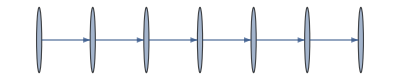
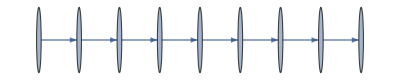
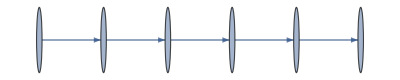
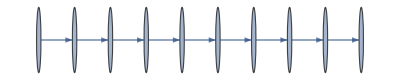
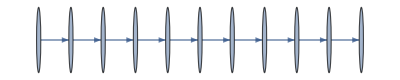
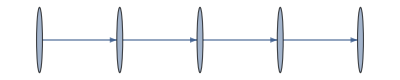

```mathematica
paths=Graph[DirectedEdge@@@Partition[#,2,1]]&/@traces
```

Combine the graphs:

```mathematica
graph=Graph[GraphUnion@@paths,];
```

Equivalent expressions converge to the same connected component:

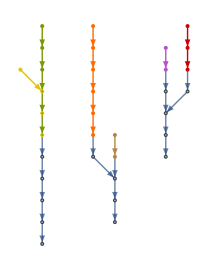

```mathematica
HighlightGraph[graph,paths]
```

Group the expressions into their corresponding equivalence class:

```mathematica
grouped=GroupBy[expressions,ToCanonicalForm]
```

<|Table[Table[S1∷ℤ,{S2∷ℤ,1,2+S1∷ℤ,1}],{S1∷ℤ,1,5,1}]→{Table[i,{i,5},{j,i+2}],Table[ConstantArray[i,i+2],{i,5}]},Table[Table[S1∷ℤ,{S1∷ℤ,1,2+S2∷ℤ,1}],{S2∷ℤ,1,5,1}]→{Array[Range,5,3],Range/@Range[3,7]},Table[Table[S1∷ℤ,{S1∷ℤ,1,S2∷ℤ,1}],{S2∷ℤ,1,10,1}]⟦2⟧→{First[Rest[Range/@Range[10]]],Table[Table[j,{j,i}],{i,10}]⟦2⟧}|>

```mathematica
TableForm[KeyValueMap[Reverse@*List,grouped]]
```

Table[i,{i,5},{j,i+2}]
Table[ConstantArray[i,i+2],{i,5}] | Table[Table[S1∷ℤ,{S2∷ℤ,1,2+S1∷ℤ,1}],{S1∷ℤ,1,5,1}]
Array[Range,5,3]
Range/@Range[3,7] | Table[Table[S1∷ℤ,{S1∷ℤ,1,2+S2∷ℤ,1}],{S2∷ℤ,1,5,1}]
First[Rest[Range/@Range[10]]]
Table[Table[j,{j,i}],{i,10}]⟦2⟧ | Table[Table[S1∷ℤ,{S1∷ℤ,1,S2∷ℤ,1}],{S2∷ℤ,1,10,1}]⟦2⟧

## Source & Additional Information

### Creator

Richard Hennigan <richardh@wolfram.com>

### Source Control Repository

https://github.com/rhennigan/CodeEquivalenceUtilities

### Keywords

code equivalence

code transformations

equivalent input

same code

canonical

transform code

exercises

code quiz

grading

### Categories

Cloud & Deployment |  Core Language & Structure
 Data Manipulation & Analysis |  Engineering Data & Computation
 External Interfaces & Connections |  Financial Data & Computation
 Geographic Data & Computation |  Geometry
 Graphs & Networks |  Higher Mathematical Computation
 Images |  Knowledge Representation & Natural Language
 Machine Learning |  Notebook Documents & Presentation
 Scientific and Medical Data & Computation |  Social, Cultural & Linguistic Data
 Sound & Video |  Strings & Text
 Symbolic & Numeric Computation |  System Operation & Setup
 Time-Related Computation |  User Interface Construction
 Visualization & Graphics |

### Related Resource Objects

SameExpressionShapeQ

SameInstanceQ

SameAsQ

CheckMatch

DefinitionData

EvaluationTiming

ExpressionLineDiff

ReplaceContext

### Source/Reference Citation

Source, reference or citation information

### Links

Wolfram Videos - Determining Code Equivalence for Automated Grading

Wolfram Videos - Wolfram Challenges: Behind the Scenes

Wolfram Challenges: Programming Puzzles for the Wolfram Language

An Elementary Introduction to the Wolfram Language - Online Exercises

### Compatibility

#### Wolfram Language Version

12.2+

#### Operating System

Windows |  Mac |  Unix

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

#### Environments

SessionLocal or cloud interactive session |  ScriptScript run in batch mode |  SubkernelParallel or grid subkernel
 WebEvaluationCloud evaluation initiated by an HTTP request |  WebAPIAPI called through an HTTP request |  ScheduledScheduled task
 BatchJobRemote batch job |  |

#### Cloud Support

Supported in cloud

## Author Notes

Additional information about limitations, issues, etc.